## 最小作用量原理

```mathematica
<<VariationalMethods`
```

## 最小作用量的优势

### 示例 1

在任意时刻 ，列尼在  处定位乔治的原点， 描述乔治如何相对于列尼运动
在  时刻发生的一个时间，列尼赋以坐标 ，乔治赋以坐标

```mathematica
EulerEquations[1/2 m(X'[t]+f'[t])^2-V[X[t]],X[t],t]//FullSimplify
```

V'[X[t]]+m (f''[t]+X''[t])==0

乔治观测到了一个额外的等于  的施加在物体上的“虚拟”力

### 示例 2

乔治在正在旋转的旋转木马上，列尼坐标系由  组成，而乔治的坐标系由  组成

假设列尼观察到质点运动时没有力施加在上面

```mathematica
lcs2=m/2(D[X[t]Cos[ω t]+Y[t]Sin[ω t],t]^2+D[-X[t]Sin[ω t]+Y[t]Cos[ω t],t]^2)//FullSimplify//Expand//Collect[#,{m ω^2/2,m ω,m/2}]&(*将拉格朗日量分为三项：离心力、科里奥利力、动能*)
```

1/2 m ω^2 (X[t]^2+Y[t]^2)+m ω (Y[t] X'[t]-X[t] Y'[t])+1/2 m (X'[t]^2+Y'[t]^2)

```mathematica
EulerEquations[lcs2,{X[t],Y[t]},t]//FullSimplify (*包含离心力和科里奥利力的牛顿方程*)
```

{m ω^2 X[t]==m (2 ω Y'[t]+X''[t]),m ω (ω Y[t]+2 X'[t])==m Y''[t]}

### 练习3

试将乔治的运动方程变换到极坐标下

```mathematica
llx3=m/2(D[R[t] Cos[θ[t]],t]^2+D[R[t] Sin[θ[t]],t]^2)//Simplify
```

1/2 m (R'[t]^2+R[t]^2 θ'[t]^2)

```mathematica
EulerEquations[llx3,{R[t],θ[t]},t]//FullSimplify
```

{m R[t] θ'[t]^2==m R''[t],m R[t] (2 R'[t] θ'[t]+R[t] θ''[t])==0}

### 练习5

长度为  的单摆运动

```mathematica
eqlx5=EulerEquations[1/2 m l^2 θ'[t]^2+m g l Cos[θ[t]],θ[t],t];
DSolve[eqlx5,θ[t],t]
```

Solve::ifun: Solve 正在使用反函数，因此可能无法找到某些解；请使用 Reduce 来获取完整的解信息.

{{θ[t]→2 JacobiAmplitude[(√(2 g+l C[1]) (t+C[2]))/(2 √l),(4 g)/(2 g+l C[1])]},{θ[t]→-2 JacobiAmplitude[(t √(2 g+l C[1]))/(2 √l)+(√(2 g+l C[1]) C[2])/(2 √l),(4 g)/(2 g+l C[1])]}}

## 对称性和守恒定律

## 双摆运动

-Graphics-连杆长1米、摆锤质量为1千克，第一个摆离开垂直方向的角度为 ，第二个摆相对于第一个摆偏离角度

```mathematica
x1[t_]=Sin[θ[t]];y1[t_]=Cos[θ[t]];x2[t_]=x1[t]+Sin[α[t]+θ[t]];y2[t_]=y1[t]+Cos[α[t]+θ[t]];
```

第一个摆锤的动能

```mathematica
t1=1/2(x1'[t]^2+y1'[t]^2)//Simplify
```

1/2 θ'[t]^2

第二个摆锤的动能

```mathematica
t2=1/2(x2'[t]^2+y2'[t]^2)//Simplify
```

1/2 α'[t]^2+(1+Cos[α[t]]) α'[t] θ'[t]+(1+Cos[α[t]]) θ'[t]^2

总势能为

```mathematica
V[θ_,α_]:=-g(2Cos[θ]+Cos[θ-α])
```

考虑和不考虑重力场时拉格朗日量为

```mathematica
l1=t1+t2
l2=t1+t2-V[θ[t],α[t]]
```

1/2 α'[t]^2+(1+Cos[α[t]]) α'[t] θ'[t]+1/2 θ'[t]^2+(1+Cos[α[t]]) θ'[t]^2

g (Cos[α[t]-θ[t]]+2 Cos[θ[t]])+1/2 α'[t]^2+(1+Cos[α[t]]) α'[t] θ'[t]+1/2 θ'[t]^2+(1+Cos[α[t]]) θ'[t]^2

### 练习6

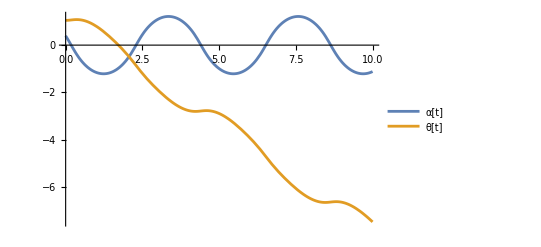

```mathematica
sol1=NDSolve[{EulerEquations[l1,{α[t],θ[t]},t],α[0]==Pi/8,α'[0]==-2,θ[0]==Pi/3,θ'[0]==0},{α[t],θ[t]},{t,0,10}];Plot[{α[t],θ[t]}/.sol1//Evaluate,{t,0,10},PlotLegends->{"α[t]","θ[t]"}]
```

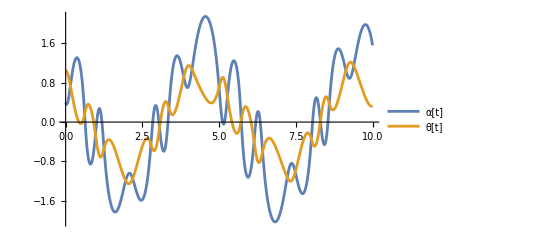

```mathematica
sol2=NDSolve[{EulerEquations[l2/.g->9.8,{α[t],θ[t]},t],α[0]==Pi/8,α'[0]==-2,θ[0]==Pi/3,θ'[0]==0},{α[t],θ[t]},{t,0,10}];Plot[{α[t],θ[t]}/.sol2//Evaluate,{t,0,10},PlotLegends->{"α[t]","θ[t]"}]
```

```mathematica
Table[Evaluate@GraphicsRow@{Graphics[{{PointSize[.025],{Red,Point[{x1[t],-y1[t]}]},{Blue,Point[{x2[t],-y2[t]}]},Line[{{0,0},{x1[t],-y1[t]},{x2[t],-y2[t]}}]}/. sol1},PlotRange->{{-2,2},{-2,2}}],
Graphics[{{PointSize[.025],{Red,Point[{x1[t],-y1[t]}]},{Blue,Point[{x2[t],-y2[t]}]},Line[{{0,0},{x1[t],-y1[t]},{x2[t],-y2[t]}}]}/. sol2},PlotRange->{{-2,2},{-2,2}}]},
{t,0,10,.025}];
Export["双摆.gif",%]
(*由于坐标系的问题，y轴坐标加个负号*)
```

双摆.gif

## 哈密顿力学与时间不变性

## 简谐振子的哈密顿函数

### 练习1

将  代换  得到

```mathematica
m D[q[t](k m)^(-1/4),t]^2/2-k (q[t](k m)^(-1/4))^2/2
```

-(k q[t]^2)/(2 √(k m))+(m q'[t]^2)/(2 √(k m))

```mathematica
Solve[{k/Sqrt[k m]==ω,m/Sqrt[k m]==1/ω},ω,Assumptions->m>0](*得到ω与k,m的关系*)
```

{{ω→(√k)/(√m)}}

### 练习2

代换前后能量守恒，即 ，则 
，

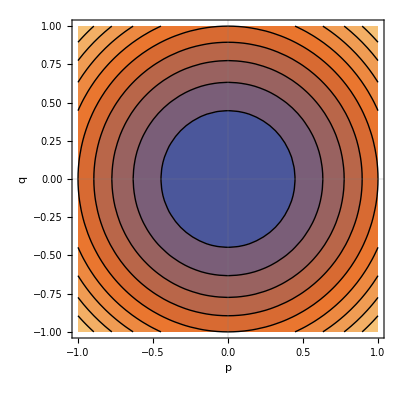

```mathematica
ContourPlot[p^2+q^2,{p,-1,1},{q,-1,1},PlotTheme->"Scientific",FrameLabel->{"p","q"}]
```

对于一般的机械系统，能量曲面形式非常复杂而无法进行可视化，但是原理是相同的：
能量曲面一层一层地填充相空间，流体在能量曲面上流动，相点一直保持在它初始的曲面上